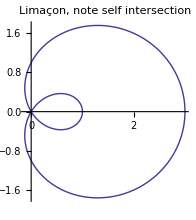

```mathematica
(* Simon Schmidt 2012 *)
lim[t_]:={Cos[t](1+2Cos[t]),Sin[t](1+2Cos[t])}
limnorm[t_]:=Evaluate[Normalize[D[lim[t],t]].{{0,-1},{1,0}}]
ParametricPlot[lim[t],{t,-Pi,Pi},
AspectRatio->Automatic,
PlotLabel->"Limaçon, note self intersection"]
Animate[
ParametricPlot[
Evaluate[{lim[2t],lim[t]+0.03*limnorm[t]}],{t,0,tmax},
PlotRange->{{-1,3.2},{-2,2}},
PlotLabel->"Same curve with different speed of parametrization"],{tmax,0.01,2Pi},AnimationRunning->False]
```

For any signed (smooth) function k(s) there exists a curve with that signed curvature,
Example:
k(s)=s
let s_0=0,  we get:
ρ(s)=∫_0^s u du =s^2/2  so:

```mathematica
ClearAll[γ]
```

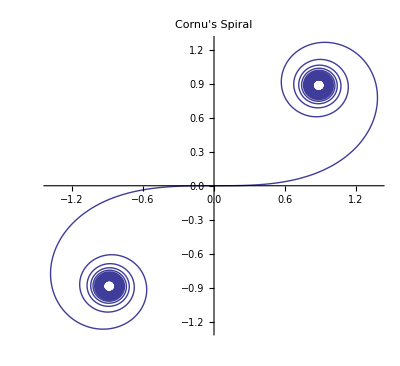

```mathematica
γ[s_]:=Evaluate[{
Integrate[Cos[t^2/2],{t,0,s}],
Integrate[Sin[t^2/2],{t,0,s}]
}];
ParametricPlot[γ[s],{s,-20,20},PlotLabel->"Cornu's Spiral"]
```

Another example:
Want curve with
κ(s) = Cos[s]
Let γ'[s] = {Cos ρ, Sin ρ}
Since: κ_s=(d ρ)/(d s) we get
ρ=Sin[s]
and

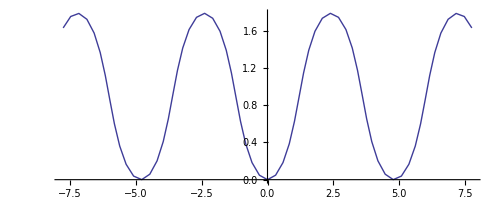

```mathematica
γ[s_]:= {
NIntegrate[Cos[Sin[t]],{t,0,s},AccuracyGoal->2,PrecisionGoal->2],
NIntegrate[Sin[Sin[t]],{t,0,s},AccuracyGoal->2,PrecisionGoal->2]
}
ParametricPlot[γ[s],{s,-10,10},PlotPoints->2]
```

General case:
Same computational method can be applied to arbitrary function
first solve the differential equation to get ρ, use this to calculate the primitive of the tangent,
this is the desired parametrization
ρ̇=k
ṫ={Cos[ρ],Sin[ρ]}
γ̇=t

InterpolatingFunction[{{-5.,5.}},<>]

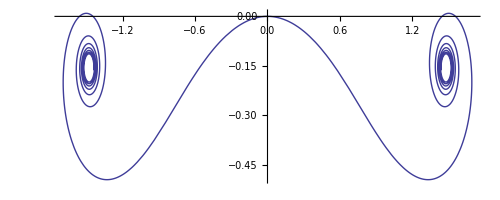

```mathematica
ClearAll[γ,κ,ρ]
curveFromCurvature[κ_,range_:{-5,5},ρ0_:0]:=Module[{ρ,t,γ},
γ/.First[NDSolve[{
ρ'[s]==κ[s],
γ'[s]=={Cos[ρ[s]],Sin[ρ[s]]},
γ[0]=={0,0},
ρ[0]==ρ0},
{γ,ρ},{s,First[range],Last[range]}]]
]
κ[s_]:=s^2-Cos[s]
γ=curveFromCurvature[κ]
ParametricPlot[γ[t],{t,-5,5}]
```

Generalizing into ℝ^3
Using the Frenet-Serret equations
(ṫ
ṅ
ḃ)=(0 | κ | 0
-κ | 0 | τ
0 | -τ | 0)(t
n
b) 
With the extra condition:
γ̇=t
and the inition conditions:
t[0]={1,0,0}
n[0]={0,1,0}
b[0]={0,0,1}
γ[0]={0,0,0}

We can get a curve γ with any desired curvature and torsion by solving this equation system.

```mathematica
ClearAll[k,s,t,g,γ]
κ[s_]:=s*Cos[1]
τ[s_]:=s-Cos[s]
g[s_]:=Evaluate[Module[{t,g,n,b},
γ[s]/.First[NDSolve[{
t'[s]==κ[s] n[s],
n'[s]== -κ[s] t[s] + τ[s]b[s],
b'[s] == -τ[s]n[s],
γ'[s]==t[s],
γ[0]=={0,0,0},
t[0]=={1,0,0},
n[0]=={0,1,0},
b[0]=={0,0,1}},
{γ[s],t[s],n[s],b[s]},{s,-10,10}]]]]
ParametricPlot3D[g[s],{s,-10,10}]
```

-Graphics3D-

```mathematica
curveFromTorsion[κ_,τ_,range_:{-1,1}]:=Module[{t,γ,n,b},
γ/.First[NDSolve[{
t'[s]==κ[s] n[s],
n'[s]== -κ[s] t[s] + τ[s]b[s],
b'[s] == -τ[s]n[s],
γ'[s]==t[s],
γ[0]=={0,0,0},
t[0]=={1,0,0},
n[0]=={0,1,0},
b[0]=={0,0,1}},
{γ,t,n,b},{s,First[range],Last[range]}]]]
```

```mathematica
κ[s_]:=Cos[s]^3 s^2
τ[s_]:=Sin[s]Cos[s] s^2
γ=curveFromTorsion[κ,τ,{-10,10}];
ParametricPlot3D[γ[t],{t,-10,10},PlotStyle->Thick]
```

-Graphics3D-

```mathematica
ClearAll[k1,k2,γ,γ1,γ2]
k[s_]:= 4.2 + Cos[s]Sin[s];
t[s_]:=Sin[s];
γ=curveFromTorsion[k,t,{-55,100}];
ParametricPlot3D[γ[t],{t,-55,100},PerformanceGoal->"Quality"]
```

-Graphics3D-